```mathematica
(*The dispersion relation*)
$Assumptions->{v≥0,0≤u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
params={(*ϵ->-x,Subscript[ϵ, l]->-x,g->√u*)ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]};
Ο=(Ν/.disp⟦1⟧)/.params//Simplify;
X=(Ν/.disp⟦2⟧)/.params//Simplify;
Clear[a,b,c,disp,params]
```

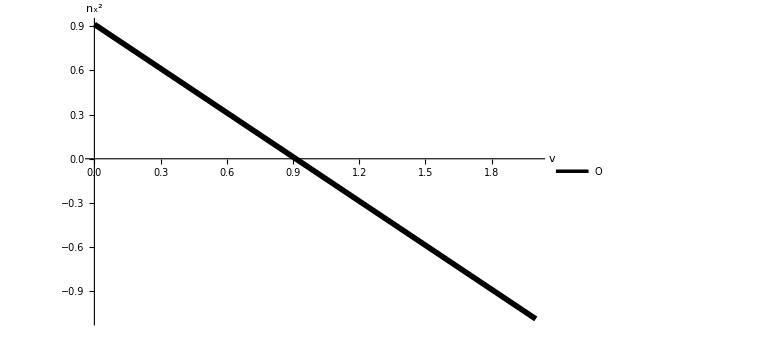

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/dispersionRelations/isotropism.png

```mathematica
(*u=0*)
params={u->0,θ->0.3,η->0};
Plot[{Ο/.params},{v,0,2},
PlotStyle->{Black,Thickness[0.007]},
PlotRange->{All,Automatic},
PlotLegends->Placed[{"O"},Scaled[{0.8,0.8}]],
ImageSize->Large,
AxesLabel->{Style["v",FontSize->45,Black],Style["n_x^2",FontSize->45,Black]},
LabelStyle->{Gray,FontSize->25}]
SaveData[config["dispersionRelations","directory"]<>"isotropism.png",%,"PNG"]
Clear[params];
```

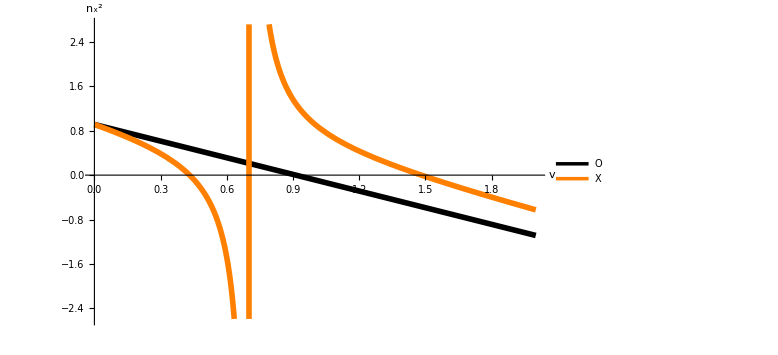

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/dispersionRelations/eta.png

```mathematica
(*η=0*)
params={u->0.3,θ->0.3,η->0};
Plot[{Ο/.params,X/.params},{v,0,2},
PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]}},
PlotRange->{All,Automatic},
PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.7}]],
ImageSize->Large,
AxesLabel->{Style["v",FontSize->45,Black],Style["n_x^2",FontSize->45,Black]},
LabelStyle->{FontSize->25}]
SaveData[config["dispersionRelations","directory"]<>"eta.png",%,"PNG"]
Clear[params];
```

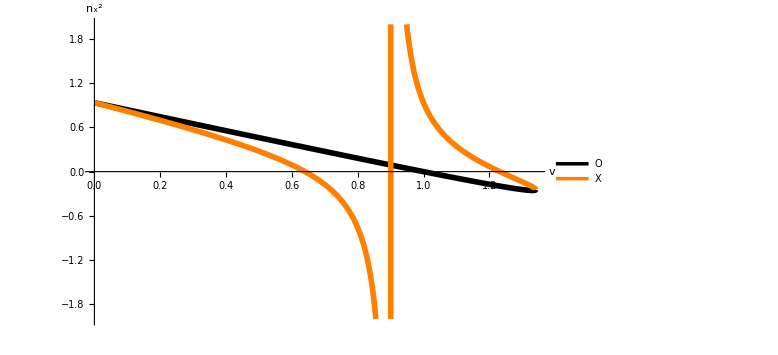

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/dispersionRelations/teta.png

```mathematica
(*θ=0*)
params={u->υ,θ->0,η->0.5ArcSin[√(√υ/(1+√υ))]}/.υ->0.1;
Plot[{Ο/.params,X/.params},{v,0,2},
PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]}},
PlotRange->{All,{-2,2}},
PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],
ImageSize->Large,
AxesLabel->{Style["v",FontSize->45,Black],Style["n_x^2",FontSize->45,Black]},
LabelStyle->{FontSize->25}]
SaveData[config["dispersionRelations","directory"]<>"teta.png",%,"PNG"]
Clear[params];
```

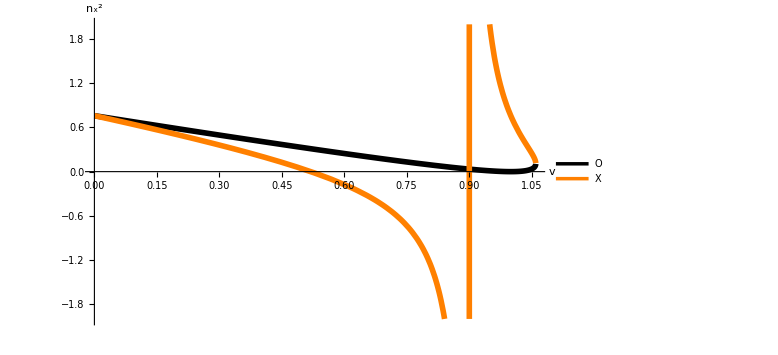

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/dispersionRelations/optimum.png

```mathematica
params={u->υ,θ->0,η->ArcSin[√(√υ/(1+√υ))]}/.υ->0.1;
Plot[{Ο/.params,X/.params},{v,0,2},
PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]}},
PlotRange->{All,{-2,2}},
PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.8}]],
ImageSize->Large,
AxesLabel->{Style["v",FontSize->45,Black],Style["n_x^2",FontSize->45,Black]},
LabelStyle->{FontSize->25}]
SaveData[config["dispersionRelations","directory"]<>"optimum.png",%,"PNG"]
Clear[params];
```

```mathematica
$Assumptions->{v≥0,0≤u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
params={ϵ->-x,Subscript[ϵ, l]->-x,g->√u(*ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u)*),Subscript[n, y]->0(*Cos[θ]Sin[η]*),Subscript[n, z]->Sin[θ]};
Οl=(Ν/.disp⟦1⟧)/.params//Simplify;
Xl=(Ν/.disp⟦2⟧)/.params//Simplify;
Clear[a,b,c,disp,params]
```

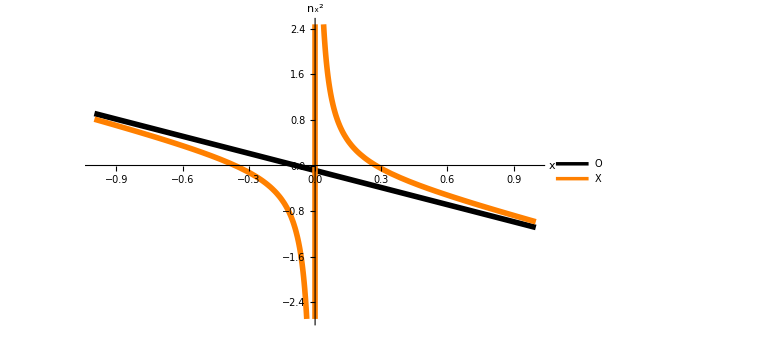

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/dispersionRelations/linearized.png

```mathematica
(*η=0*)
params={u->0.1,θ->0.3};
Plot[{Οl/.params,Xl/.params},{x,-1,1},
PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]}},
PlotRange->{All,Automatic},
PlotLegends->Placed[{"Ο","X"},Scaled[{0.8,0.8}]],
ImageSize->Large,
AxesLabel->{Style["x",FontSize->45,Black],Style["n_x^2",FontSize->45,Black]},
LabelStyle->{FontSize->25}]
SaveData[config["dispersionRelations","directory"]<>"linearized.png",%,"PNG"]
Clear[params];
```